```mathematica
a=1;
Manipulate[Plot[{Re[1/Sqrt[Sqrt[Pi]*(a+(I T)/a)]*Exp[-1/(2*a^2 (1+(I T)/a^2))*x^2]],Im[1/Sqrt[Sqrt[Pi]*(a+(I T)/a)]*Exp[-1/(2*a^2 (1+(I T)/a^2))*x^2]],Re[1/Sqrt[Sqrt[Pi]*(a+(I T)/a)]*Exp[-1/(2*a^2 (1+(I T)/a^2))*x^2]]^2+Im[1/Sqrt[Sqrt[Pi]*(a+(I T)/a)]*Exp[-1/(2*a^2 (1+(I T)/a^2))*x^2]]^2},{x,-6,6},PlotRange->{-1,1},PlotLegends->{"Real","Imaginary","Probability Density"},Filling->{3-> Axis},PlotLabel->TextString@Row@{"T=",T}],{T,0,15,0.01}]
```

```mathematica
Anim=Table[Plot[{Re[1/Sqrt[Sqrt[Pi]*(a+(I T)/a)]*Exp[-1/(2*a^2 (1+(I T)/a^2))*x^2]],Im[1/Sqrt[Sqrt[Pi]*(a+(I T)/a)]*Exp[-1/(2*a^2 (1+(I T)/a^2))*x^2]],Re[1/Sqrt[Sqrt[Pi]*(a+(I T)/a)]*Exp[-1/(2*a^2 (1+(I T)/a^2))*x^2]]^2+Im[1/Sqrt[Sqrt[Pi]*(a+(I T)/a)]*Exp[-1/(2*a^2 (1+(I T)/a^2))*x^2]]^2},{x,-10,10},PlotRange->{-1,1},PlotLegends->{"Real","Imaginary","Probability Density"},Filling->{3-> Axis},PlotLabel->TextString@Row@{"T=",T}],{T,0,30,0.5}];
Export["animSize1200.gif",Anim,ImageSize->1200,"CompressionLevel"->0]
```

animSize1200.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["anim.gif"]]]
```

```mathematica
SystemOpen["anim.gif"]
```

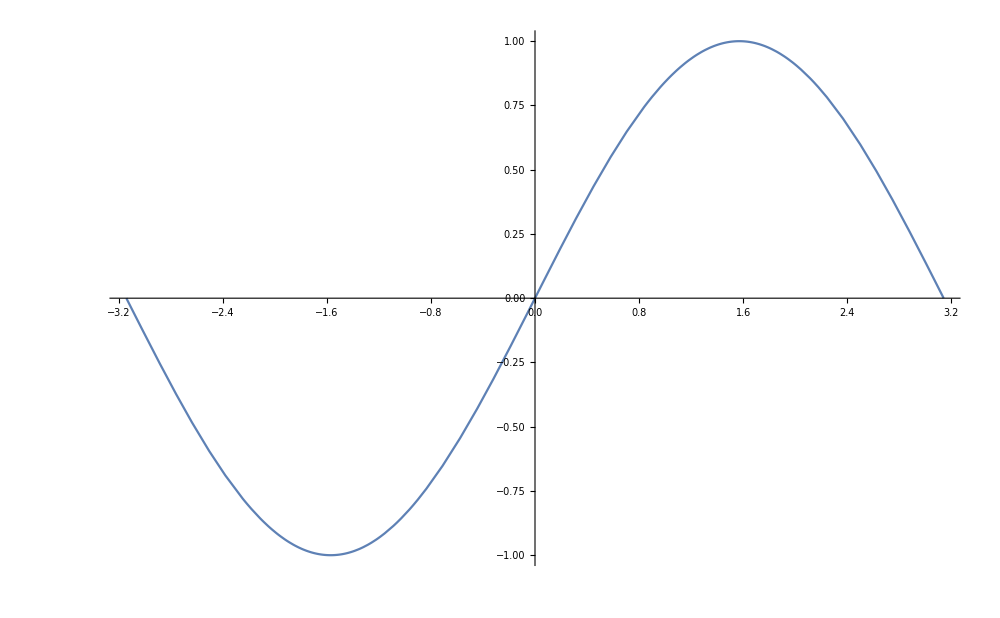

```mathematica
Plot[Sin[x],{x,-Pi,Pi},ImageSize->1000]
```

```mathematica
Export["anim1200c0.gif",Anim,ImageSize->1200,"CompressionLevel"->0]
```